```mathematica
f[x_]:=1/(k x^3 + (1-k)x + 1)
```

```mathematica
Manipulate[Plot[1/(k x^3 + (1-k)x + 1),{x,-5,5},PlotRange->10],{k,-10,10}]
```

```mathematica
(*c i*)
```

```mathematica
Manipulate[Plot[k x^3 + (1-k)x + 1,{x,-10,10},PlotRange->10],{k,-10,10}]
```

```mathematica
(*ci*)
```

```mathematica
Solve[k x^3 + (1-k)x + 1 == 0,k]
```

{{k→-1/((-1+x) x)}}

```mathematica
Manipulate[Plot[{-1/((-1+x) x),k},{x,-10,10},PlotRange->10],{k,-10,10}]
```

```mathematica
(*cii*)
```

```mathematica
Solve[f'[x] == 0,k]
```

{{k→1/(1-3 x^2)}}

```mathematica
f'[x]
```

-(1-k+3 k x^2)/((1+(1-k) x+k x^3)^2)

```mathematica
Manipulate[Plot[-(1-k+3 k x^2)/((1+(1-k) x+k x^3)^2), {x,-10,10},PlotRange->10],{k,-10,10}]
```

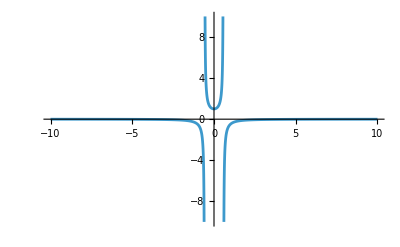

```mathematica
Plot[1/(1-3 x^2),{x,-10,10},PlotRange->10]
```

```mathematica
{x,1/(1-3 x^2)}/.Solve[D[1/(1-3 x^2),x] == 0,x]
```

{{0,1}}

```mathematica
(*ciii*)
```

```mathematica
Solve[{f[x] == -1,f'[x] == 0},{x,k},Reals]//N
```

{{x→-2.87939,k→-0.0418891},{x→-0.652704,k→-3.59627},{x→0.532089,k→6.63816}}